#### Parameters Setup.

```mathematica
k=15.1;
sampleSize=100;
trajLen=1000;
thetaMin=0.;
thetaMax=2.π;
pMin=0.;
pMax=2.π;
```

#### Evolution

```mathematica
thLis={RandomReal[{thetaMin,thetaMax},{sampleSize}]};
pLis={RandomReal[{pMin,pMax},{sampleSize}]};
Do[
AppendTo[pLis,Mod[pLis[[-1]]+k*Sin[thLis[[-1]]],2.*π]];
AppendTo[thLis,Mod[thLis[[-1]]+pLis[[-1]],2.*π]];
,{trajLen}]
```

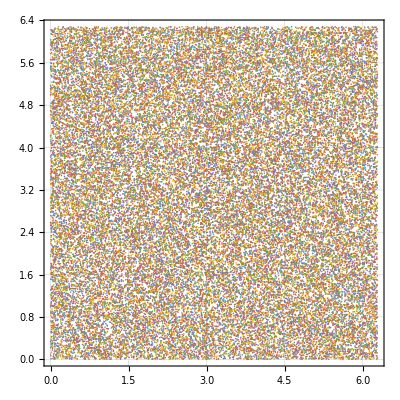

```mathematica
tb=Table[Transpose[{thLis[[;;,i]],pLis[[;;,i]]}],{i,1,sampleSize}];
ListPlot[tb[[;;,1;;500]],{PlotTheme->"Detailed",AspectRatio->1}]
```

#### Momentum Distribution

```mathematica
thLis={RandomReal[{thetaMin,thetaMax},{sampleSize}]};
pLis={RandomReal[{pMin,pMax},{sampleSize}]};
Do[
AppendTo[pLis,pLis[[-1]]+K*Sin[thLis[[-1]]]];
AppendTo[thLis,Mod[thLis[[-1]]+pLis[[-1]],2.*π]];
,{trajLen}]
```

```mathematica
Manipulate[Histogram[pLis[[time]]],{time,1,trajLen,1}]
```

Histogram::ldata: 4.94 is not a valid dataset or list of datasets.

Histogram::ldata: 2.44 is not a valid dataset or list of datasets.

Part::partd: Part specification pLis⟦495⟧ is longer than depth of object.

Histogram::ldata: pLis⟦495⟧ is not a valid dataset or list of datasets.

Part::partw: Part 495 of {{0.33,0.629199,0.33,0.629199},{1.92599,2.22519,1.88845,2.18765},«47»,{-0.202914,-1.4057,1.95851,2.06596},«251»} does not exist.

Histogram::ldata: {{0.33,0.629199,0.33,0.629199},{1.92599,2.22519,1.88845,2.18765},«47»,{-0.202914,-1.4057,1.95851,2.06596},«251»}⟦495⟧ is not a valid dataset or list of datasets.

Histogram::ldata: -0.552509 is not a valid dataset or list of datasets.

Part::partw: Part 495 of {{0.33,0.629199,0.33,0.629199},{-2.9607,-2.6615,-3.0311,-2.7319},«47»,{2.09203,0.955563,-1.0999,0.620701},«251»} does not exist.

Histogram::ldata: {{0.33,0.629199,0.33,0.629199},{-2.9607,-2.6615,-3.0311,-2.7319},«47»,{2.09203,0.955563,-1.0999,0.620701},«251»}⟦495⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification pLis⟦495⟧ is longer than depth of object.

Histogram::ldata: pLis⟦495⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification pLis⟦495⟧ is longer than depth of object.

Histogram::ldata: pLis⟦495⟧ is not a valid dataset or list of datasets.

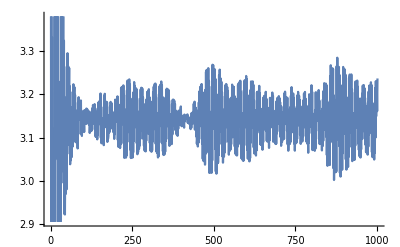

```mathematica
ListLinePlot[Mean/@pLis]
```

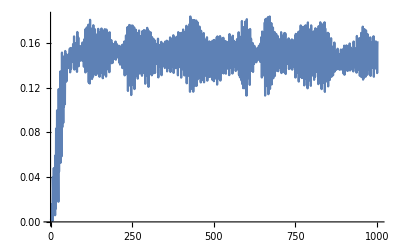

```mathematica
ListLinePlot[Variance/@pLis]
```